# Foosball game analysis

## Get Data

```mathematica
singlesRaw = Import["https://docs.google.com/spreadsheet/ccc?key=1wPZclPCCTRxLpADlaru2yhlssleeLQSe7MfPSpzuY34&output=csv"];

threadSingles[line_]:= <|
"Date" -> DateObject[line⟦1⟧, TimeZone->0],
"Red Name" -> line⟦2⟧,
"Red Score" -> line⟦3⟧,
"Blue Name" -> line⟦4⟧,
"Blue Score" -> line⟦5⟧  |>

singles = Dataset [threadSingles /@ singlesRaw⟦2;;⟧];
```

## Process

#### Time of the day

```mathematica
t = TimeObject/@singles⟦All, "Date"⟧
```

{ 16:25,16:51,12:18,13:33,13:45,13:53,14:04,⋯_57 }
1 level | 64elementsDataset[{__TimeObject}]

```mathematica
timeInSeconds[date_]:=(AbsoluteTime@TimeObject[date] - AbsoluteTime@TimeObject[{0,0,0}, TimeZone->0])
```

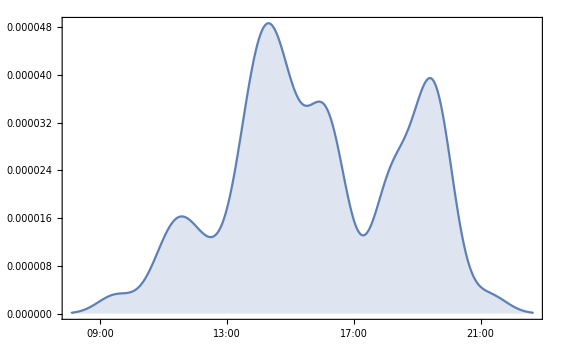

```mathematica
ticks = {timeInSeconds[#], DateString[ #,{"Hour24",":","Minute"}]}&/@ 
( TimeObject[{#,0,0},TimeZone->0]&/@ Range[1, 24, 2] );

SmoothHistogram[
timeInSeconds/@singles⟦All, "Date"⟧  ,2000,

Filling->Bottom,
Frame -> True,
FrameTicks->{{True,None},{ticks,None}}
]
```